```mathematica
<<Notation`
Symbolize[Subscript[c, s]]
Symbolize[Subscript[τ, c]]
```

## Analytical solution of torsional shock

```mathematica
ClearAll[R1,T,γ,λ,f,g]
```

```mathematica
Subscript[𝒟, R][u_,R_,τ_]:=D[u[R,τ],{R,2}]+1/R D[u[R,τ],R]-u[R,τ]/R^2
Subscript[𝒟, τ][u_,R_,τ_]:=D[u[R,τ],{τ,2}]
γ[m_]=BesselJZero[1,m];
λ[n_]=(2π n)/T;
f[n_]:=Cos[λ[n]#2]+Sin[λ[n]#2]&
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0, γ[m]]&
```

### Check eigenfunctions

```mathematica
Subscript[𝒟, R][g[m],R,τ]+γ[m]^2 g[m][R,τ]//FullSimplify
Subscript[𝒟, τ][f[n],R,τ]+λ[n]^2 f[n][R,τ]//FullSimplify
```

0

0

### Check orthonormality

```mathematica
fx=Table[Integrate[f[n1][R,τ]f[n2][R,τ],{τ,0,T}],{n1,10},{n2,10}]
```

{{T,0,0,0,0,0,0,0,0,0},{0,T,0,0,0,0,0,0,0,0},{0,0,T,0,0,0,0,0,0,0},{0,0,0,T,0,0,0,0,0,0},{0,0,0,0,T,0,0,0,0,0},{0,0,0,0,0,T,0,0,0,0},{0,0,0,0,0,0,T,0,0,0},{0,0,0,0,0,0,0,T,0,0},{0,0,0,0,0,0,0,0,T,0},{0,0,0,0,0,0,0,0,0,T}}

```mathematica
gx=Table[Integrate[R *g[n1][R,τ]g[n2][R,τ],{R,0,1}],{n1,10},{n2,10}]
```

{{-BesselJ[2,BesselJZero[1,1]]/BesselJ[0,BesselJZero[1,1]],0,0,0,0,0,0,0,0,0},{0,-BesselJ[2,BesselJZero[1,2]]/BesselJ[0,BesselJZero[1,2]],0,0,0,0,0,0,0,0},{0,0,-BesselJ[2,BesselJZero[1,3]]/BesselJ[0,BesselJZero[1,3]],0,0,0,0,0,0,0},{0,0,0,-BesselJ[2,BesselJZero[1,4]]/BesselJ[0,BesselJZero[1,4]],0,0,0,0,0,0},{0,0,0,0,-BesselJ[2,BesselJZero[1,5]]/BesselJ[0,BesselJZero[1,5]],0,0,0,0,0},{0,0,0,0,0,-BesselJ[2,BesselJZero[1,6]]/BesselJ[0,BesselJZero[1,6]],0,0,0,0},{0,0,0,0,0,0,-BesselJ[2,BesselJZero[1,7]]/BesselJ[0,BesselJZero[1,7]],0,0,0},{0,0,0,0,0,0,0,-BesselJ[2,BesselJZero[1,8]]/BesselJ[0,BesselJZero[1,8]],0,0},{0,0,0,0,0,0,0,0,-BesselJ[2,BesselJZero[1,9]]/BesselJ[0,BesselJZero[1,9]],0},{0,0,0,0,0,0,0,0,0,-BesselJ[2,BesselJZero[1,10]]/BesselJ[0,BesselJZero[1,10]]}}

```mathematica
Diagonal[gx]//N
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Check R Bessel expansion

```mathematica
γ[m_]=N@BesselJZero[1,m];
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0, γ[m]]&;
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
BJR[R_,1]= BJC[1]g[1][R];
BJR[R_,mm_]:=BJR[R,mm]=BJR[R,mm-1]+BJC[mm]g[mm][R];
BJR[R_]=BJR[R,#]&/@{10,20,30,40};
```

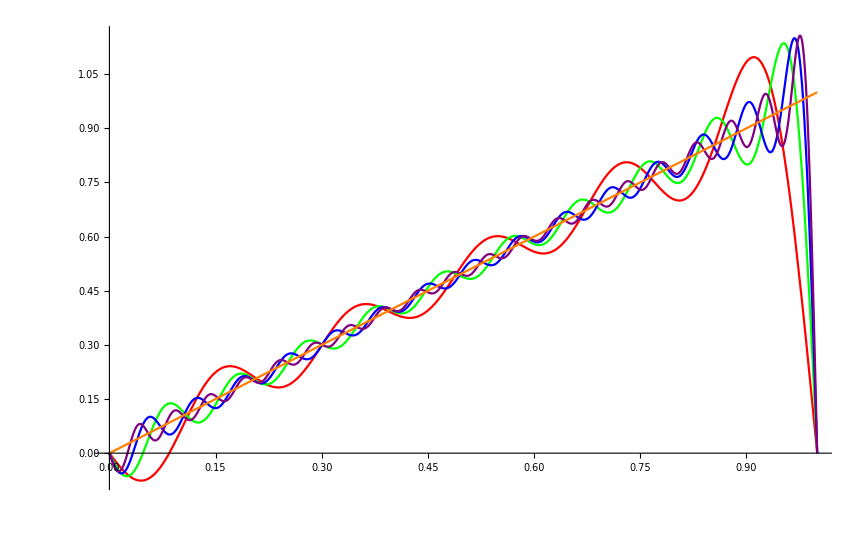

```mathematica
Plot[Evaluate@Append[BJR[R],R],{R,0,1},PlotStyle->{Red,Green,Blue,Purple,Orange},PlotRange->All]
```

### Check Ωpp[t] Fourier expansion

0.0497529 Sin[(π t)/5]+0.098035 Sin[(2 π t)/5]+0.143434 Sin[(3 π t)/5]+0.18465 Sin[(4 π t)/5]+0.220547 Sin[π t]+0.250198 Sin[(6 π t)/5]+0.272912 Sin[(7 π t)/5]+0.288263 Sin[(8 π t)/5]+0.296097 Sin[(9 π t)/5]+0.296532 Sin[2 π t]+0.289945 Sin[(11 π t)/5]+0.276948 Sin[(12 π t)/5]+0.258356 Sin[(13 π t)/5]+0.235144 Sin[(14 π t)/5]+0.2084 Sin[3 π t]+0.179279 Sin[(16 π t)/5]+0.148946 Sin[(17 π t)/5]+0.118532 Sin[(18 π t)/5]+0.0890862 Sin[(19 π t)/5]+0.0615379 Sin[4 π t]

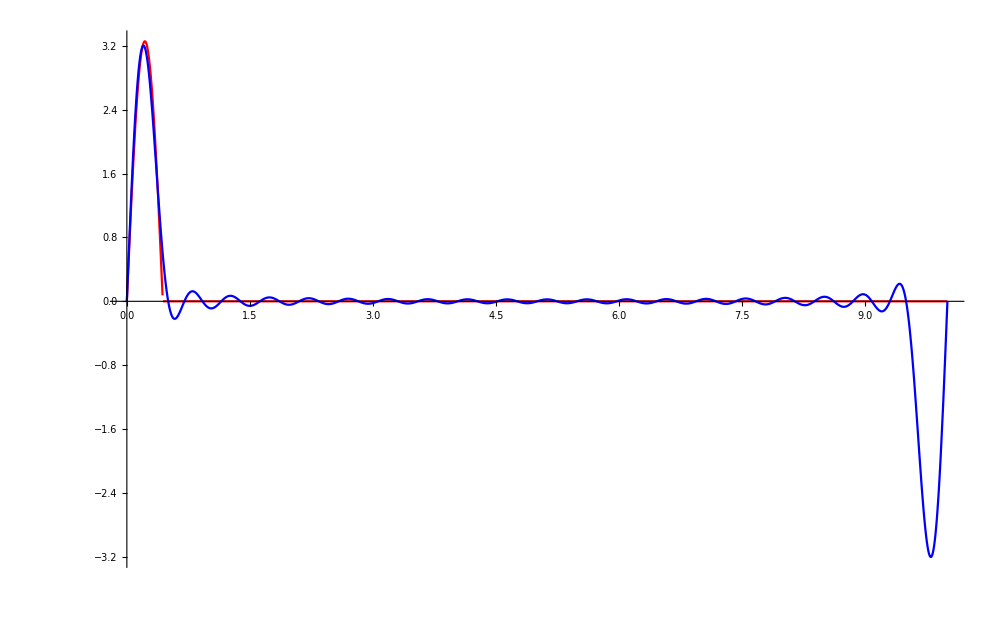

```mathematica
Block[{MM = 30,NN=20(*,λ =8500*),T =10 ,μ=34000,ρ=1040,R1=0.0652543,r0  =0.000001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
]
(*Ωpp[t_]=1000 Sin[ 100  c t];*)
(*Ωpp[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];*)
ΩppD[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];
Ωpp[τ_]=Simplify[ΩppD[τ Subscript[τ, c]] Subscript[τ, c]^2];
(*Ωpp[t_]=1000 Cos[ 400 t];*)
T=10;
FSC[n_]:=FourierSinCoefficient[Ωpp[t],t,n,FourierParameters->{1,2π/T}]
(*FCΩpp[t_]=Sum[FCC[n]Cos[(2n π)/T t],{n,20}]*)
FSΩpp[t_]=Sum[FSC[n]Sin[(2n π)/T t],{n,20}]
Plot[{Ωpp[t],(*FCΩpp[t],*)FSΩpp[t]},{t,0,T},PlotStyle->{Red,Blue,Green},PlotRange->All]
```

### Dimensionless solution

```mathematica
Block[{MM = 30,NN=20(*,λ =8500*),T =10 ,μ=34000,ρ=1040,R1=0.0652543,r0  =0.000001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FSC,BJC,B,A,a,sol*)},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
(*Ωpp[t_]=1000 Cos[ 400 t];*)
(*Ωpp[τ_]=1000 Sin[ 100 R1 τ ];*)
ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];
Ωpp[τ_]=ΩppReal[τ Subscript[τ, c]] Subscript[τ, c]^2;
γ[m_]=N@BesselJZero[1,m];
λ[n_]=(2.0π n)/T;
f[n_]=Sin[λ[n] #2]&;
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0,γ[m]]&;
FSC[n_]:=FourierSinCoefficient[Ωpp[τ],τ,n,FourierParameters->{1,2.0π/T}];
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
B[m_,n_]:=-BJC[m]FSC[n];
A[m_,n_]:=B[m,n]/(γ[m]^2-λ[n]^2);
a[m_]:=Sum[A[m,n]λ[n],{n,NN}]/( γ[m]);
u[R_,τ_]=Sum[ g[m][R,τ] Sum[A[m,n]f[n][R,τ],{n,NN}],{m,MM}];
v[R_,τ_]=Sum[-a[m] g[m][R,τ] Sin[ γ[m]τ],{m,MM}];
sol[R_,τ_]=Chop[Simplify[u[R,τ]+v[R,τ]],10^-7];
RealSol[R_,τ_] = R1 sol[R/R1 ,τ/Subscript[τ, c] ];
ShortRealSol[R_,τ_]=Chop[RealSol[R,τ] ,10^-4]

]
```

0.0652543 (0.475019 BesselJ[1,58.7196 R] Sin[335.742 τ]-0.165716 BesselJ[1,107.511 R] Sin[614.72 τ]+0.0740648 BesselJ[1,155.905 R] Sin[891.421 τ]-0.000379904 BesselJ[1,155.905 R] (1. Sin[55.0546 τ]+1.99334 Sin[110.109 τ]+2.97402 Sin[165.164 τ]+3.93748 Sin[220.218 τ]+4.88144 Sin[275.273 τ]+5.80704 Sin[330.328 τ]+6.72052 Sin[385.382 τ]+7.63586 Sin[440.437 τ]+8.57936 Sin[495.491 τ]+9.59861 Sin[550.546 τ]+10.7816 Sin[605.6 τ]+12.3027 Sin[660.655 τ]+14.5565 Sin[715.71 τ]+18.6548 Sin[770.764 τ]+29.4333 Sin[825.819 τ]+152.596 Sin[880.873 τ]-29.1382 Sin[935.928 τ]-10.0627 Sin[990.983 τ]-4.73161 Sin[1046.04 τ]-2.34364 Sin[1101.09 τ])+0.000967978 BesselJ[1,107.511 R] (1. Sin[55.0546 τ]+2.01942 Sin[110.109 τ]+3.08231 Sin[165.164 τ]+4.22361 Sin[220.218 τ]+5.50024 Sin[275.273 τ]+7.01376 Sin[330.328 τ]+8.96482 Sin[385.382 τ]+11.8101 Sin[440.437 τ]+16.8533 Sin[495.491 τ]+29.876 Sin[550.546 τ]+196.285 Sin[605.6 τ]-35.6172 Sin[660.655 τ]-14.4874 Sin[715.71 τ]-8.19454 Sin[770.764 τ]-5.16331 Sin[825.819 τ]-3.39331 Sin[880.873 τ]-2.25304 Sin[935.928 τ]-1.47815 Sin[990.983 τ]-0.937016 Sin[1046.04 τ]-0.555577 Sin[1101.09 τ])-0.00451299 BesselJ[1,58.7196 R] (1. Sin[55.0546 τ]+2.14854 Sin[110.109 τ]+3.70106 Sin[165.164 τ]+6.33853 Sin[220.218 τ]+13.1605 Sin[275.273 τ]+152.952 Sin[330.328 τ]-16.8088 Sin[385.382 τ]-7.82094 Sin[440.437 τ]-4.91618 Sin[495.491 τ]-3.43408 Sin[550.546 τ]-2.51644 Sin[605.6 τ]-1.88606 Sin[660.655 τ]-1.42573 Sin[715.71 τ]-1.07702 Sin[770.764 τ]-0.807139 Sin[825.819 τ]-0.595978 Sin[880.873 τ]-0.430253 Sin[935.928 τ]-0.300614 Sin[990.983 τ]-0.200119 Sin[1046.04 τ]-0.123376 Sin[1101.09 τ])-0.000113518 BesselJ[1,252.407 R] (1. Sin[55.0546 τ]+1.97909 Sin[110.109 τ]+2.91693 Sin[165.164 τ]+3.79428 Sin[220.218 τ]+4.59352 Sin[275.273 τ]+5.29911 Sin[330.328 τ]+5.89794 Sin[385.382 τ]+6.37964 Sin[440.437 τ]+6.7368 Sin[495.491 τ]+6.965 Sin[550.546 τ]+7.06289 Sin[605.6 τ]+7.03197 Sin[660.655 τ]+6.8764 Sin[715.71 τ]+6.60262 Sin[770.764 τ]+6.21888 Sin[825.819 τ]+5.73451 Sin[880.873 τ]+5.15912 Sin[935.928 τ]+4.50133 Sin[990.983 τ]+3.76689 Sin[1046.04 τ]+2.95544 Sin[1101.09 τ])+0.000193094 BesselJ[1,204.181 R] (1. Sin[55.0546 τ]+1.9837 Sin[110.109 τ]+2.93526 Sin[165.164 τ]+3.8397 Sin[220.218 τ]+4.68338 Sin[275.273 τ]+5.4543 Sin[330.328 τ]+6.14251 Sin[385.382 τ]+6.74036 Sin[440.437 τ]+7.24279 Sin[495.491 τ]+7.64756 Sin[550.546 τ]+7.95546 Sin[605.6 τ]+8.17064 Sin[660.655 τ]+8.30107 Sin[715.71 τ]+8.35943 Sin[770.764 τ]+8.36501 Sin[825.819 τ]+8.34798 Sin[880.873 τ]+8.36007 Sin[935.928 τ]+8.50596 Sin[990.983 τ]+9.06067 Sin[1046.04 τ]+11.1736 Sin[1101.09 τ])-0.0153367 BesselJ[1,204.181 R] Sin[1167.45 τ]+0.00491335 BesselJ[1,252.407 R] Sin[1443.19 τ]-0.0023598 BesselJ[1,300.606 R] Sin[1718.78 τ]+0.00131784 BesselJ[1,348.791 R] Sin[1994.29 τ]-0.000807272 BesselJ[1,396.965 R] Sin[2269.73 τ]+0.000527644 BesselJ[1,445.133 R] Sin[2545.14 τ]-0.000362087 BesselJ[1,493.296 R] Sin[2820.53 τ]+0.000258151 BesselJ[1,541.456 R] Sin[3095.89 τ]-0.000189823 BesselJ[1,589.613 R] Sin[3371.24 τ]+0.000143193 BesselJ[1,637.768 R] Sin[3646.58 τ]-0.000110368 BesselJ[1,685.921 R] Sin[3921.91 τ])

```mathematica
Block[{ μ=34000,ρ=1040
(*,c,Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
R1=0.0652543;
r0  =0.000001;
tend=0.1;
Subscript[c, s]=Sqrt[μ/ρ];
(*Ωpp[t_]=Piecewise[{{1000 Sin[ 100 t],0≤t≤π/100.},{0,t>π/100.}}];*)
ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];
(*Ωpp[t_]=1000 Cos[ 500 t];*)
uθNSol=NDSolve[{
1/r^2 Subscript[c, s]^2 (-uθ[r,t]+r (Derivative[1,0][uθ][r,t]+r Derivative[2,0][uθ][r,t]))-r ΩppReal[t] ==Derivative[0,2][uθ][r,t],
uθ[r,0]==0,
Derivative[0,1][uθ][r,0]==0,
uθ[R1,t]==0
},uθ,{r,r0,R1},{t,0,tend}]
]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 38.8464 at t = 0.1 in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{uθ→                             -6
InterpolatingFunction[{{1. 10  , 0.0652543}, {0., 0.1}}, <>]}}

```mathematica
Manipulate[
Show[
Plot[{uθ[r,t]/.uθNSol[[1]],ShortRealSol[r,t]},{r,0.0001,R1},PlotRange->{-0.025,0.025},PlotStyle->{Directive[Red],Directive[Blue,Dashed],Green,Black}]
],{t,0,0.05}]
```

Plot::plln: Limiting value R1 in {r,0.0001,R1} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value R1 in {r,0.0001,R1} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

## Comparison with Yang’s simulation

### Periodic load solution

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
<<"Data/Ulist.mx"
```

```mathematica
time1=Import["Data/time1.txt",{"Data"}][[;;,7]];
```

```mathematica
time1[[2;;]]-time1[[1;;-2]]
```

{0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.,0.0001,0.}

#### Check Ωpp[t] Fourier expansion

```mathematica
Block[{MM = 30,NN=20(*,λ =8500*) ,μ=34000,ρ=1040,R1=0.0652543,r0  =0.000001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
T =10;
(*ΩppD[τ_]=1000 Sin[ 100. Subscript[c, s] τ ];*)
ΩppD[τ_]=Piecewise[{{2000Exp[1-1/(1-(τ/0.004142-1)^2)],0≤τ≤0.008284},{0,τ>0.008284}}];
Ωpp[τ_]=Simplify[ΩppD[τ Subscript[τ, c]] Subscript[τ, c]^2]
]
```

Piecewise[{{0., τ>0.725861||τ<0}, {0.708104 ⅇ^(0.131719/(τ (-0.725861+1. τ))), True}}]

$Aborted

General::munfl: Exp[-888.542] is too small to represent as a normalized machine number; precision may be lost.

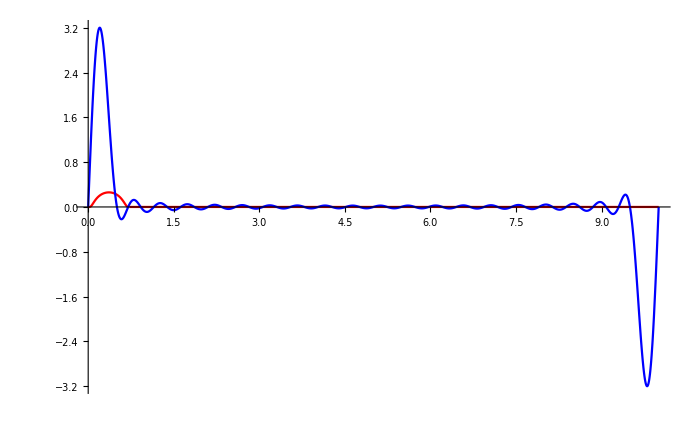

```mathematica
FSC[n_]:=FourierSinCoefficient[Ωpp[t],t,n,FourierParameters->{1,2.0*π/T}]
(*FCΩpp[t_]=Sum[FCC[n]Cos[(2n π)/T t],{n,20}]*)
FSΩpp[t_]=Sum[FSC[n]Sin[(2.0n π)/T t],{n,20}]
Plot[{Ωpp[t],(*FCΩpp[t],*)FSΩpp[t]},{t,0,T},PlotStyle->{Red,Blue,Green},PlotRange->All]
```

#### Check solution

```mathematica
Block[{MM=30,NN=20(*,λ =8500*),T =10,μ=34000,ρ=1040,R1=0.0652543,r0 =0.0001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FSC,BJC,B,A,a,sol*)
},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
tend=0.18;
ΩppReal[τ_]=1000 Sin[ 100.0  τ ];
(*ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];*)
(*
(*ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];*)
Ωpp[τ_]=ΩppReal[τ Subscript[τ, c]] Subscript[τ, c]^2;
γ[m_]=N@BesselJZero[1,m];
λ[n_]=(2.π n)/T;
f[n_]=Sin[λ[n] #2]&;
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0,γ[m]]&;
FSC[n_]:=FourierSinCoefficient[Ωpp[τ],τ,n,FourierParameters->{1,2.0π/T}];
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
B[m_,n_]:=-BJC[m]FSC[n];
A[m_,n_]:=B[m,n]/(γ[m]^2-λ[n]^2);
a[m_]:=Sum[A[m,n]λ[n],{n,NN}]/( γ[m]);
u[R_,τ_]=Sum[ g[m][R,τ] Sum[A[m,n]f[n][R,τ],{n,NN}],{m,MM}];
v[R_,τ_]=Sum[-a[m] g[m][R,τ] Sin[ γ[m]τ],{m,MM}];
sol[R_,τ_]=Chop[Simplify[u[R,τ]+v[R,τ]],10^-7];
RealSol[R_,τ_] = R1 sol[R/R1 ,τ/Subscript[τ, c] ];
ShortRealSol[R_,τ_]=Chop[RealSol[R,τ] ,10^-4];*)
uθNSol=NDSolve[{
1/r^2 Subscript[c, s]^2 (-uθ[r,t]+r (Derivative[1,0][uθ][r,t]+r Derivative[2,0][uθ][r,t]))-r ΩppReal[t] ==Derivative[0,2][uθ][r,t],
uθ[r,0]==0,
Derivative[0,1][uθ][r,0]==0,
uθ[R1,t]==0
},uθ,{r,r0,R1},{t,0,tend}]
]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 349.22 at t = 0.18 in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{uθ→InterpolatingFunction[{{0.0001, 0.0652543}, {0., 0.18}}, <>]}}

```mathematica
Manipulate[
Show[
Ulist[[n]]
,Plot[{uθ[r,time1[[n]]]/.uθNSol[[1]],RealSol[r,time1[[n]]]},{r,0.0001,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
]
,{n,1,Length@time1,1}]
```

Part::partd: Part specification Ulist⟦1⟧ is longer than depth of object.

Part::partd: Part specification time1⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[Ulist⟦1⟧,].

Part::partd: Part specification Ulist⟦1⟧ is longer than depth of object.

Part::partd: Part specification time1⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[Ulist⟦1⟧,].

Part::partd: Part specification Ulist⟦1⟧ is longer than depth of object.

Plot::plln: Limiting value R1 in {r,0.0001,R1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Ulist⟦1⟧,Plot[{uθ[r,time1⟦FE`n$$1577⟧]/.uθNSol⟦1⟧,RealSol[r,time1⟦FE`n$$1577⟧]},{r,0.0001,R1},PlotStyle→{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]].

Part::partd: Part specification Ulist⟦1⟧ is longer than depth of object.

Plot::plln: Limiting value R1 in {r,0.0001,R1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Ulist⟦1⟧,Plot[{uθ[r,time1⟦FE`n$$1577⟧]/.uθNSol⟦1⟧,RealSol[r,time1⟦FE`n$$1577⟧]},{r,0.0001,R1},PlotStyle→{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]].

#### Make video

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
Table[
plt=Show[
Ulist[[n]]
,Plot[{uθ[r,time1[[n]]]/.uθNSol[[1]],RealSol[r,time1[[n]]]},{r,0.0001,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
];
Export["Fig/plt"<>IntegerString[n]<>".png",plt]
,{n,1,500,1}]
```

### Sine Bump function solution

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
UlistBump//Dimensions
```

{314,83,2}

```mathematica
DumpSave["Data/UlistBump.mx",UlistBump];
```

```mathematica
<<"Data/UlistBump.mx"
```

```mathematica
time2=Import["Data/time2.txt",{"Data"}][[;;,7]];
```

```mathematica
time2[[2;;]]-time2[[;;-2]]
```

{2.×10^-6,2.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,4.×10^-6,5.×10^-6,7.×10^-6,6.×10^-6,7.×10^-6,6.×10^-6,7.×10^-6,6.×10^-6,7.×10^-6,7.×10^-6,6.×10^-6,8.×10^-6,0.000011,0.000012,0.000012,0.000012,0.000013,0.000015,0.000015,0.000015,0.000015,0.000015,0.000015,0.000019,0.000019,0.000023,0.000023,0.000029,0.000029,0.000037,0.000045,0.000052,0.000052,0.000064,0.000041,0.00004,0.000032,0.000032,0.000033,0.000032,0.000039,0.00004,0.00004,0.00004,0.00005,0.00004,0.00006,0.00007,0.00007,0.00008,0.00009,0.00012,0.00015,0.0001,0.0001,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.00007,0.00007,0.00006,0.00007,0.00008,0.00009,0.00009,0.00009,0.00009,0.00011,0.00014,0.00013,0.00014,0.00016,0.00017,0.00021,0.00005,0.00004,0.00004,0.00006,0.00006,0.00007,0.00007,0.00007,0.00008,0.00007,0.00009,0.00008,0.00009,0.0001,0.0001,0.00012,0.00012,0.00013,0.00014,0.00016,0.00015,0.00019,0.00019,0.00022,0.00022,0.00026,0.00027,0.00032,0.00032,0.00041,0.0004,0.00012,0.00014,0.00019,0.00023,0.00029,0.0003,0.0003,0.0003,0.0002,0.0003,0.0003,0.0003,0.0003,0.0003,0.0001,0.,0.0001,0.0001,0.0002,0.0001,0.0001,0.0002,0.0001,0.0001,0.0001,0.0002,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0002,0.0001,0.0001,0.0002,0.0001,0.0001,0.0002,0.0001,0.0002,0.0001,0.0002,0.0002,0.0002,0.0001,0.0002,0.0003,0.0002,0.0002,0.0003,0.0002,0.0003,0.0003,0.0002,0.0003,0.0003,0.0003,0.0003,0.0003,0.0001,0.,0.0001,0.0001,0.0001,0.0001,0.0002,0.0001,0.0002,0.0001,0.0002,0.0001,0.0002,0.0002,0.0001,0.0002,0.0002,0.0003,0.0002,0.0002,0.0003,0.0003,0.0003,0.0003,0.0004,0.0003,0.0004,0.0005,0.0005,0.0005,0.0001,0.0002,0.0001,0.0002,0.0003,0.0003,0.,0.0001,0.0001,0.0001,0.0001,0.0002,0.0002,0.0002,0.0002,0.0003,0.0002,0.0003,0.0003,0.0003,0.0004,0.0001,0.0001,0.0002,0.0002,0.0003,0.0004,0.0003,0.0004,0.0003,0.0004,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0003,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0004,0.0003,0.0004,0.0004,0.0001,0.0001,0.0002,0.0002,0.0003,0.0002,0.0003,0.0003,0.0003,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0001,0.0002,0.0002,0.0001,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0002,0.0003,0.0002,0.0003,0.0003,0.0003,0.0003,0.0004,0.0002}

#### Check Ωpp[t] Fourier expansion

```mathematica
Block[{MM = 30,NN=20(*,λ =8500*) ,μ=34000,ρ=1040,R1=0.0652543,r0  =0.000001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
T =10;
ΩppD[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];
Ωpp[τ_]=Simplify[ΩppD[τ Subscript[τ, c]] Subscript[τ, c]^2]
]
```

Piecewise[{{0., τ>0.43811||τ<0}, {3.25621 Sin[7.17078 τ], True}}]

0.0497529 Sin[0.628319 t]+0.098035 Sin[1.25664 t]+0.143434 Sin[1.88496 t]+0.18465 Sin[2.51327 t]+0.220547 Sin[3.14159 t]+0.250198 Sin[3.76991 t]+0.272912 Sin[4.39823 t]+0.288263 Sin[5.02655 t]+0.296097 Sin[5.65487 t]+0.296532 Sin[6.28319 t]+0.289945 Sin[6.9115 t]+0.276948 Sin[7.53982 t]+0.258356 Sin[8.16814 t]+0.235144 Sin[8.79646 t]+0.2084 Sin[9.42478 t]+0.179279 Sin[10.0531 t]+0.148946 Sin[10.6814 t]+0.118532 Sin[11.3097 t]+0.0890862 Sin[11.9381 t]+0.0615379 Sin[12.5664 t]

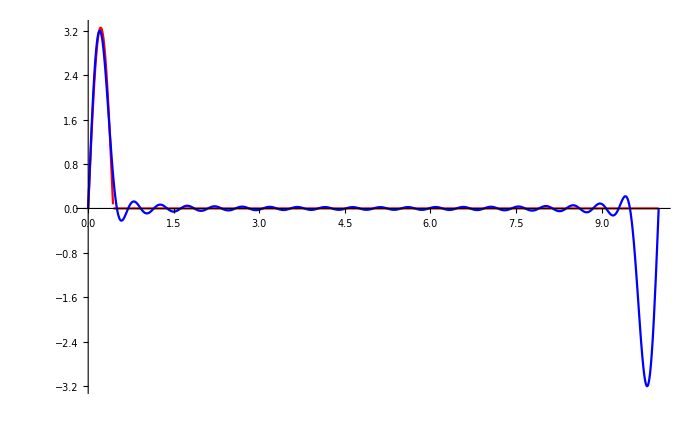

```mathematica
FSC[n_]:=FourierSinCoefficient[Ωpp[t],t,n,FourierParameters->{1,2.0*π/T}]
(*FCΩpp[t_]=Sum[FCC[n]Cos[(2n π)/T t],{n,20}]*)
FSΩpp[t_]=Sum[FSC[n]Sin[(2.0n π)/T t],{n,20}]
Plot[{Ωpp[t],(*FCΩpp[t],*)FSΩpp[t]},{t,0,T},PlotStyle->{Red,Blue,Green},PlotRange->All]
```

#### Check solution

```mathematica
Block[{MM=30,NN=20(*,λ =8500*),T =10,μ=34000,ρ=1040,R1=0.0652543,r0 =0.0001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FSC,BJC,B,A,a,sol*)
},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
tend=0.08;
(*ΩppReal[τ_]=1000 Sin[ 100.0 Subscript[c, s] τ ];*)
ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];
Ωpp[τ_]=ΩppReal[τ Subscript[τ, c]] Subscript[τ, c]^2;
γ[m_]=N@BesselJZero[1,m];
λ[n_]=(2.π n)/T;
f[n_]=Sin[λ[n] #2]&;
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0,γ[m]]&;
FSC[n_]:=FourierSinCoefficient[Ωpp[τ],τ,n,FourierParameters->{1,2.0π/T}];
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
B[m_,n_]:=-BJC[m]FSC[n];
A[m_,n_]:=B[m,n]/(γ[m]^2-λ[n]^2);
a[m_]:=Sum[A[m,n]λ[n],{n,NN}]/( γ[m]);
u[R_,τ_]=Sum[ g[m][R,τ] Sum[A[m,n]f[n][R,τ],{n,NN}],{m,MM}];
v[R_,τ_]=Sum[-a[m] g[m][R,τ] Sin[ γ[m]τ],{m,MM}];
sol[R_,τ_]=Chop[Simplify[u[R,τ]+v[R,τ]],10^-7];
RealSol[R_,τ_] = R1 sol[R/R1 ,τ/Subscript[τ, c] ];
ShortRealSol[R_,τ_]=Chop[RealSol[R,τ] ,10^-4];
uθNSol=NDSolve[{
1/r^2 Subscript[c, s]^2 (-uθ[r,t]+r (Derivative[1,0][uθ][r,t]+r Derivative[2,0][uθ][r,t]))-r ΩppReal[t] ==Derivative[0,2][uθ][r,t],
uθ[r,0]==0,
Derivative[0,1][uθ][r,0]==0,
uθ[R1,t]==0
},uθ,{r,r0,R1},{t,0,tend}];

]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 64.1067 at t = 0.08 in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
DumpSave["Data/uθNSol.mx",uθNSol];
DumpSave["Data/ShortRealSol.mx",ShortRealSol];
```

```mathematica
Manipulate[
Show[
ListPlot[UlistBump[[n]],PlotStyle->{{RGBColor[0/255,0/255,0/255],Thickness[.006],Opacity[1.0]}},
ImageSize->600,
PlotRange->{-0.015,0.015},
PlotLabel->Style["t="<>ToString[time[[n]]]<>"s",FontSize->20,FontFamily->"Times New Roman"],
PlotMarkers->{Graphics[{EdgeForm[{RGBColor[0/255,0/255,0/255]}],FaceForm[],Disk[]}],8},
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->15,FontFamily->"Times New Roman"},
FrameLabel->{Style["R (m)",FontSize->20,FontFamily->"Times New Roman"],Style["U_Θ (m)",FontSize->20,FontFamily->"Times New Roman"]}
]
,Plot[{uθ[r,time[[n]]]/.uθNSol[[1]],ShortRealSol[r,time[[n]]]},{r,r0,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
]
,{n,1,314,1}]
```

#### Make video

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
Table[
plt=Show[
ListPlot[UlistBump[[n]],PlotStyle->{{RGBColor[0/255,0/255,0/255],Thickness[.006],Opacity[1.0]}},
ImageSize->600,
PlotRange->{-0.015,0.015},
PlotLabel->Style["t="<>ToString[time[[n]]]<>"s",FontSize->20,FontFamily->"Times New Roman"],
PlotMarkers->{Graphics[{EdgeForm[{RGBColor[0/255,0/255,0/255]}],FaceForm[],Disk[]}],8},
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->15,FontFamily->"Times New Roman"},
FrameLabel->{Style["R (m)",FontSize->20,FontFamily->"Times New Roman"],Style["U_Θ (m)",FontSize->20,FontFamily->"Times New Roman"]}
]
,Plot[{uθ[r,time[[n]]]/.uθNSol[[1]],ShortRealSol[r,time[[n]]]},{r,r0,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
];
Export["Fig2/plt"<>IntegerString[n]<>".png",plt]
,{n,1,314,1}]
```

### Exp Bump function solution

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
<<"Data/utheta.mx"
```

```mathematica
UlistExp = ArrayReshape[utheta[[;;,3]],{500,83}];
```

```mathematica
time3 = utheta[[1;;-1;;83,1]];
```

```mathematica
time3[[-1]]
```

0.05

```mathematica
UlistExp//Dimensions
```

{500,83}

#### Check Ωpp[t] Fourier expansion

```mathematica
Block[{MM = 30,NN=20(*,λ =8500*) ,μ=34000,ρ=1040,R1=0.0652543,r0  =0.000001
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
T =10;
ΩppD[t_]=Piecewise[{{2000Exp[1-1/(1-(t/0.004142-1)^2)],0≤t≤0.008284},{0,t>0.008284}}];
Ωpp[τ_]=Simplify[ΩppD[τ Subscript[τ, c]] Subscript[τ, c]^2]
]
```

Piecewise[{{0., τ>0.725861||τ<0}, {0.708104 ⅇ^(0.131719/(τ (-0.725861+1. τ))), True}}]

0.0102755 Sin[0.628319 t]+0.0197729 Sin[1.25664 t]+0.0277911 Sin[1.88496 t]+0.0337743 Sin[2.51327 t]+0.0373639 Sin[3.14159 t]+0.038428 Sin[3.76991 t]+0.0370659 Sin[4.39823 t]+0.0335877 Sin[5.02655 t]+0.0284724 Sin[5.65487 t]+0.022309 Sin[6.28319 t]+0.0157295 Sin[6.9115 t]+0.00934072 Sin[7.53982 t]+0.00366404 Sin[8.16814 t]-0.000911817 Sin[8.79646 t]-0.00415889 Sin[9.42478 t]-0.00601775 Sin[10.0531 t]-0.00658516 Sin[10.6814 t]-0.00608472 Sin[11.3097 t]-0.00482544 Sin[11.9381 t]-0.00315431 Sin[12.5664 t]

General::munfl: Exp[-888.542] is too small to represent as a normalized machine number; precision may be lost.

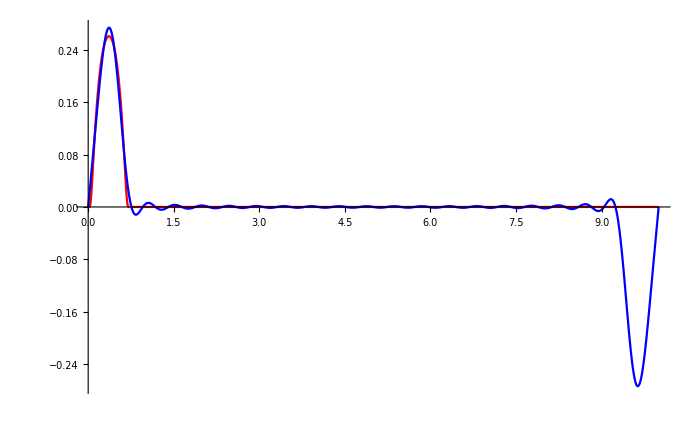

```mathematica
(*FSC[n_]:=FourierSinCoefficient[Ωpp[t],t,n,FourierParameters->{1,2.0*π/T}]*)
FSC[n_]:=4./T NIntegrate[Ωpp[t] Sin[(2.0 n  π)/T t ],{t,0,T/2}]
(*FCΩpp[t_]=Sum[FCC[n]Cos[(2n π)/T t],{n,20}]*)
FSΩpp[t_]=Sum[FSC[n]Sin[(2.0n π)/T t],{n,20}]
Plot[{Ωpp[t],(*FCΩpp[t],*)FSΩpp[t]},{t,0,T},PlotStyle->{Red,Blue,Green},PlotRange->All]
```

#### Check solutionU

```mathematica
Block[{MM=30,NN=50(*,λ =8500*),T =10,μ=34000,ρ=1040
(*,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FSC,BJC,B,A,a,sol*)
},
R1=0.0652543;
r0 =0.0001;
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
tend=0.08;
(*ΩppReal[τ_]=1000 Sin[ 100.0 Subscript[c, s] τ ];*)
(*ΩppReal[t_]=Piecewise[{{25000Sin[(t π)/0.005],0≤t≤0.005},{0,t>0.005}}];*)
ΩppReal[t_]=Piecewise[{{2000Exp[1-1/(1-(t/0.004142-1)^2)],0<t≤0.008284},{0,t>0.008284}}];
(*Ωpp[τ_]=ΩppReal[τ Subscript[τ, c]] Subscript[τ, c]^2;
γ[m_]=N@BesselJZero[1,m];
λ[n_]=(2.π n)/T;
f[n_]=Sin[λ[n] #2]&;
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0,γ[m]]&;
(*FSC[n_]:=FourierSinCoefficient[Ωpp[τ],τ,n,FourierParameters->{1,2.0π/T}];*)
FSC[n_]:=4./T NIntegrate[Ωpp[t] Sin[(2.0 n  π)/T t ],{t,0,T/2}];
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
B[m_,n_]:=-BJC[m]FSC[n];
A[m_,n_]:=B[m,n]/(γ[m]^2-λ[n]^2);
a[m_]:=Sum[A[m,n]λ[n],{n,NN}]/( γ[m]);
u[R_,τ_]=Sum[ g[m][R,τ] Sum[A[m,n]f[n][R,τ],{n,NN}],{m,MM}];
v[R_,τ_]=Sum[-a[m] g[m][R,τ] Sin[ γ[m]τ],{m,MM}];
sol[R_,τ_]=Chop[Simplify[u[R,τ]+v[R,τ]],10^-7];
RealSol[R_,τ_] = R1 sol[R/R1 ,τ/Subscript[τ, c] ];
ShortRealSol[R_,τ_]=Chop[RealSol[R,τ] ,10^-4];*)
uθNSol=NDSolve[{
1/r^2 Subscript[c, s]^2 (-uθ[r,t]+r (Derivative[1,0][uθ][r,t]+r Derivative[2,0][uθ][r,t]))-r ΩppReal[t] ==Derivative[0,2][uθ][r,t],
uθ[r,0]==0,
Derivative[0,1][uθ][r,0]==0,
uθ[R1,t]==0
},uθ,{r,r0,R1},{t,0,tend}];

]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 261.399 at t = 0.08 in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
uθNSol
```

{{uθ→InterpolatingFunction[{{0.0001, 0.0652543}, {0., 0.08}}, <>]}}

```mathematica
Manipulate[
Show[
ListPlot[UlistExp[[n]],PlotStyle->{{RGBColor[0/255,0/255,0/255],Thickness[.006],Opacity[1.0]}},
ImageSize->600,
DataRange->{0,R1},
PlotRange->{-0.002,0.002},
PlotLabel->Style["t="<>ToString[time3[[n]]]<>"s",FontSize->20,FontFamily->"Times New Roman"],
PlotMarkers->{Graphics[{EdgeForm[{RGBColor[0/255,0/255,0/255]}],FaceForm[],Disk[]}],8},
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->15,FontFamily->"Times New Roman"},
FrameLabel->{Style["R (m)",FontSize->20,FontFamily->"Times New Roman"],Style["U_Θ (m)",FontSize->20,FontFamily->"Times New Roman"]}
]
,Plot[{(*uθ[r,time3[[n]]]/.uθNSol[[1]],*)RealSol[r,time3[[n]]]},{r,r0,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
]
,{n,1,500,1}]
```

Part::partd: Part specification UlistExp⟦121⟧ is longer than depth of object.

Part::partd: Part specification time3⟦121⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: UlistExp⟦121⟧ is not a list of numbers or pairs of numbers.

Plot::plln: Limiting value r0 in {r,r0,R1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[UlistExp⟦121⟧,PlotStyle→{{RGBColor[0, 0, 0],Thickness[0.006],Opacity[1.]}},ImageSize→600,DataRange→{0,R1},PlotRange→{-0.002,0.002},PlotLabel→t=time3[[121]]s,PlotMarkers→{,8},Frame→{{True,False},{True,False}},BaseStyle→{FontSize→15,FontFamily→Times New Roman},FrameLabel→{R (m),U_Θ (m)}],Plot[{RealSol[r,time3⟦FE`n$$1921⟧]},{r,r0,R1},PlotStyle→{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]].

#### Make video

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
Table[
plt=Show[
ListPlot[UlistExp[[n]],PlotStyle->{{RGBColor[0/255,0/255,0/255],Thickness[.006],Opacity[1.0]}},
ImageSize->600,
DataRange->{0,R1},
PlotRange->{-0.002,0.002},
PlotLabel->Style["t="<>ToString[time3[[n]]]<>"s",FontSize->20,FontFamily->"Times New Roman"],
PlotMarkers->{Graphics[{EdgeForm[{RGBColor[0/255,0/255,0/255]}],FaceForm[],Disk[]}],8},
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->15,FontFamily->"Times New Roman"},
FrameLabel->{Style["R (m)",FontSize->20,FontFamily->"Times New Roman"],Style["U_Θ (m)",FontSize->20,FontFamily->"Times New Roman"]}
]
,Plot[{(*uθ[r,time3[[n]]]/.uθNSol[[1]],*)RealSol[r,time3[[n]]]},{r,r0,R1},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Dashing[0.02],Thickness[0.006]]}]
];
Export["FigExp/plt"<>IntegerString[n]<>".png",plt]
,{n,1,500,1}]
```

#### 3D plot

```mathematica
Plt1 =ListPointPlot3D[utheta[[;;;;10]],
ImageSize->800,
LabelStyle->Directive[Black],
PlotStyle->{Gray,PointSize[Medium]},
BaseStyle->{FontSize->20,FontFamily->"Times New Roman"},
AxesLabel->{"τ (s)","R (m)","u_θ (m)"}]
```

-Graphics3D-

```mathematica
Plt2 = Plot3D[RealSol[r,t],{t,0,0.05},{r,0,R1},
ColorFunction->(Blend[{RGBColor[0.22999999999999982, 0.29899999999999977, 0.7539999999999997],RGBColor[0.2836943237507675, 0.3846393738868723, 0.8265719197385752],RGBColor[0.34128786345814, 0.46795213120396734, 0.8874939456315885],RGBColor[0.40295662302450325, 0.5474691874303457, 0.9352898575453745],RGBColor[0.46825778499999665, 0.6215505752814867, 0.9688853377433658],RGBColor[0.5362638205709569, 0.6885319032850463, 0.9876300982714906],RGBColor[0.6056937666087167, 0.7468047079174234, 0.9913051994451706],RGBColor[0.6750269913669033, 0.7948718219031321, 0.9801155288931463],RGBColor[0.7425944217361238, 0.8313907083911475, 0.9546681491396606],RGBColor[0.8066494660818774, 0.8552089878536259, 0.9159378748115107],RGBColor[0.8654236525430442, 0.8653930898068188, 0.8652220017562686],RGBColor[0.9106157890357767, 0.8380760251029263, 0.7957341087347833],RGBColor[0.9418775164378905, 0.7979621305248119, 0.7217036926051889],RGBColor[0.959080312348575, 0.745790952967169, 0.6448346795874556],RGBColor[0.9621941730899576, 0.6824495325197455, 0.5667597793674168],RGBColor[0.9513438881735578, 0.608885794307683, 0.4890097317713277],RGBColor[0.926842962151432, 0.5259522153988744, 0.41299140092015674],RGBColor[0.8892129256622827, 0.43406933155379024, 0.33997734813191627],RGBColor[0.839191796958454, 0.33229821812545196, 0.2711117064644712],RGBColor[0.7777336026329164, 0.2145348782235777, 0.207442252956191],RGBColor[0.7060000000000001, 0.015999999999998966, 0.15000000000000002]},#3]&),
ColorFunctionScaling->True,
MaxRecursion->4,Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plt= Show[Plt1,Plt2]
```

-Graphics3D-

```mathematica
Directory[]
```

/Users/wenqiangfang/Dropbox (Brown)/research/HyperElastic_Compression

```mathematica
Export["CompareExp.EPS",Plt,ImageResolution->1000]
```

CompareExp.EPS